```mathematica
(*Back substitute the auxiliary variables and get the polynomial expressions for f[u,v] and g[u,v] as in eq.17 of 2modes.pdf as of Sep 2, 2013*)
```

```mathematica
Subscript[A, 1] = Subscript[μ, 1]+ Subscript[ã, 1]*ũ + Subscript[b̃, 1]*ṽ ;
```

```mathematica
Subscript[A, 2] = Subscript[μ, 2]+ Subscript[ã, 2]*ũ + Subscript[b̃, 2]*ṽ ;
```

```mathematica
fuv = ũ * Subscript[A, 1] - ṽ * Subscript[A, 2];
```

```mathematica
guv = (Subscript[A, 1]^2-Subscript[c, 1]*ṽ)*(ũ+2*ṽ)^2 + Subscript[e, 2]^2 *ṽ^2;
```

```mathematica
scalings = { ũ-> Subscript[c, 2]*u, ṽ -> Subscript[c, 1]*v, Subscript[ã, 1] -> Subscript[a, 1]/Subscript[c, 2], Subscript[b̃, 1]->Subscript[b, 1]/Subscript[c, 1], Subscript[ã, 2]->Subscript[a, 2]/Subscript[c, 2],Subscript[b̃, 2]->Subscript[b, 2]/Subscript[c, 1]};
```

```mathematica
w[u_,v_]:=(-2*u*(u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1]))/Subscript[c, 1] 
q[u_,v_,w_]:=(-Subscript[e, 2]*w)/(2*(u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1])+(u Subscript[a, 2]+v Subscript[b, 2]+Subscript[μ, 2]))
```

```mathematica
fuv /.scalings
```

```mathematica
u Subscript[c, 2] (u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1])-v Subscript[c, 1] (u Subscript[a, 2]+v Subscript[b, 2]+Subscript[μ, 2]) (*Expression for f[u,v]*)
```

```mathematica
(*Definition of f[u,v]:*)
```

```mathematica
f[u_,v_] := u Subscript[c, 2] (u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1])-v Subscript[c, 1] (u Subscript[a, 2]+v Subscript[b, 2]+Subscript[μ, 2]);
```

```mathematica
guv/.scalings
```

```mathematica
v^2 Subscript[c, 1]^2 Subscript[e, 2]^2+(2 v Subscript[c, 1]+u Subscript[c, 2])^2 (-v Subscript[c, 1]^2+(u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1])^2)(*Expression for g[u,v]*)
```

```mathematica
(*Definition of g[u,v]*)
```

```mathematica
g[u_,v_] :=v^2 Subscript[c, 1]^2 Subscript[e, 2]^2+(2 v Subscript[c, 1]+u Subscript[c, 2])^2 (-v Subscript[c, 1]^2+(u Subscript[a, 1]+v Subscript[b, 1]+Subscript[μ, 1])^2)
```

```mathematica
(*Try to get an expression for u(v) such that f[u(v),v]=0 :*)
```

```mathematica
Solve[f[u,v]==0 , u]
```

{{u→1/(2 a_1 c_2)(v a_2 c_1-v b_1 c_2-c_2 μ_1-√((-v a_2 c_1+v b_1 c_2+c_2 μ_1)^2-4 a_1 c_2 (-v^2 b_2 c_1-v c_1 μ_2)))},{u→1/(2 a_1 c_2)(v a_2 c_1-v b_1 c_2-c_2 μ_1+√((-v a_2 c_1+v b_1 c_2+c_2 μ_1)^2-4 a_1 c_2 (-v^2 b_2 c_1-v c_1 μ_2)))}}

```mathematica
uroot1 = 1/(2 Subscript[a, 1] Subscript[c, 2])(v Subscript[a, 2] Subscript[c, 1]-v Subscript[b, 1] Subscript[c, 2]-Subscript[c, 2] Subscript[μ, 1]-√((-v Subscript[a, 2] Subscript[c, 1]+v Subscript[b, 1] Subscript[c, 2]+Subscript[c, 2] Subscript[μ, 1])^2-4 Subscript[a, 1] Subscript[c, 2] (-v^2 Subscript[b, 2] Subscript[c, 1]-v Subscript[c, 1] Subscript[μ, 2])));
```

```mathematica
uroot2 = 1/(2 Subscript[a, 1] Subscript[c, 2])(v Subscript[a, 2] Subscript[c, 1]-v Subscript[b, 1] Subscript[c, 2]-Subscript[c, 2] Subscript[μ, 1]+√((-v Subscript[a, 2] Subscript[c, 1]+v Subscript[b, 1] Subscript[c, 2]+Subscript[c, 2] Subscript[μ, 1])^2-4 Subscript[a, 1] Subscript[c, 2] (-v^2 Subscript[b, 2] Subscript[c, 1]-v Subscript[c, 1] Subscript[μ, 2])));
```

```mathematica
Subscript[F, 1][v_] := g[uroot1, v]
```

```mathematica
Subscript[F, 2][v_] := g[uroot2,v]
```

```mathematica
parswobs = {Subscript[μ, 1]-> -2.8023, Subscript[μ, 2]-> 1, Subscript[a, 1]->  -1,Subscript[a, 2] -> -2.6636, Subscript[c, 1]-> -4.1122, Subscript[c, 2]-> 1.8854, Subscript[e, 2]-> 1};
```

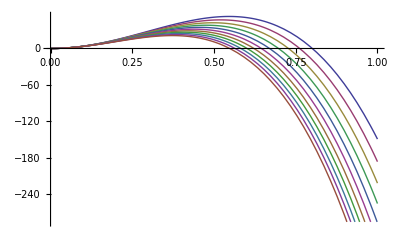

```mathematica
Plot[Evaluate[Subscript[F, 1][v]/.parswobs /. {Subscript[b, 1]-> Range[-1,0,0.1], Subscript[b, 2]->Range[-1,0,0.1]}],{v,0,1}]
```

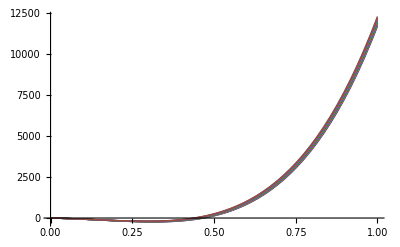

```mathematica
Plot[Evaluate[Subscript[F, 2][v]/.parswobs /. {Subscript[b, 1]-> Range[-1,0,0.1], Subscript[b, 2]->Range[-1,0,0.1]}],{v,0,1}]
```

```mathematica
Plot[Evaluate[Subscript[F, 1][v]/.parswobs /. {Subscript[b, 1]-> Range[-1,0,0.1], Subscript[b, 2]->Range[-1,0,0.1]}],{v,0,1500}]
```

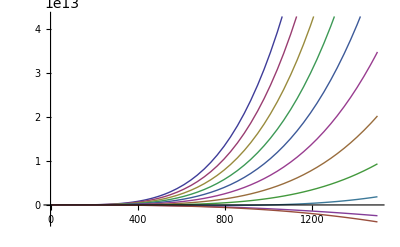

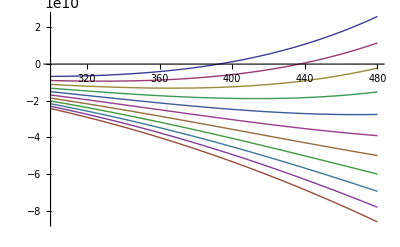

```mathematica
Plot[Evaluate[Subscript[F, 1][v]/.parswobs /. {Subscript[b, 1]-> Range[-0.2,-0.1,0.01], Subscript[b, 2]->-0.00144}],{v,300,480}]
```

```mathematica
pars85 = {Subscript[μ, 1]-> -2.8023, Subscript[μ, 2]-> 0.6128, Subscript[a, 1]->  -0.9146,Subscript[a, 2] -> -2.6636, Subscript[b, 1]->-0.20470, Subscript[b, 2]->-0.0144, Subscript[c, 1]-> -4.1122, Subscript[c, 2]-> 1.8854, Subscript[e, 2]-> 2.1769};
```

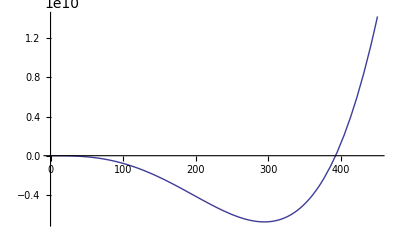

```mathematica
Plot[Evaluate[Subscript[F, 1][v]/.pars85],{v,0,450}]
```

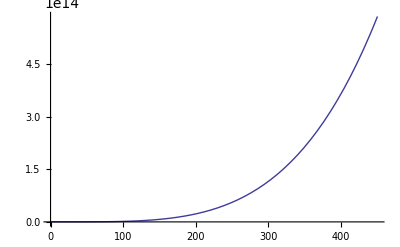

```mathematica
Plot[Evaluate[Subscript[F, 2][v]/.pars85],{v,0,450}]
```

```mathematica
NSolve[{F1[v]/.pars85}==0,v]
```

{{v→392.35},{v→0.624401},{v→1.77327×10^-32},{v→0.},{v→0.}}

```mathematica
uroot1 /. pars85 /. v->392.35043368105516
```

-1.82583

```mathematica
w[0.12327820232332917, 0.6244011441687491]/.pars85
```

-0.182442

```mathematica
q[0.12327820232332917, 0.6244011441687491, -0.18244197587542854]/.pars85
```

-0.0683543

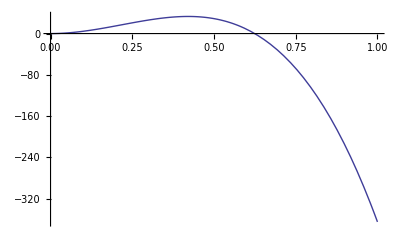

```mathematica
Plot[Evaluate[F1[v]/.pars85],{v,0,1}]
```

```mathematica
f[0.12362115821873151, 0.6286025141262683]/.pars85
```

-2.33147×10^-15

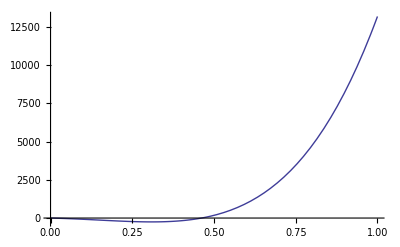

```mathematica
Plot[Evaluate[F2[v]/.pars85],{v,0,1}]
```

```mathematica
f[0, -Subscript[μ, 2]/Subscript[b, 2]]/.pars85
```

0

```mathematica
-Subscript[μ, 2]/Subscript[b, 2] /.pars85
```

425.556

```mathematica
(*Simple set of parameters*)
```

```mathematica
pars88 = {Subscript[μ, 1]-> -2.8023, Subscript[μ, 2]-> 1, Subscript[a, 1]->  -1,Subscript[a, 2] -> -2.6636, Subscript[b, 1]->0, Subscript[b, 2]->0, Subscript[c, 1]-> -4.1122, Subscript[c, 2]-> 1.8854, Subscript[e, 2]-> 1};
```

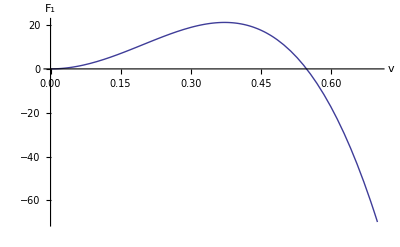

```mathematica
Plot[Evaluate[F1[v]/.pars88],{v,0,0.7}, AxesLabel->{v, Subscript[F, 1]}]
```

```mathematica
Solve[Evaluate[F1[v]/.pars88] == 0, v]
```

{{v→-2.77394×10^-9},{v→1.37621×10^-17},{v→2.77394×10^-9},{v→0.548221}}